# LHW 6

## 1. Import the matrix

```mathematica
A = Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk01.mtx.gz"];
```

### 1.1 Plot the matrix

```mathematica
MatrixPlot[A,PlotLegends->Automatic]
```

-Graphics-

### 1.2 Compute eigenvalues and eigenvectors

```mathematica
{λ,v} = Eigensystem[A];
```

#### 1.2.1 Plot Eigenvalues

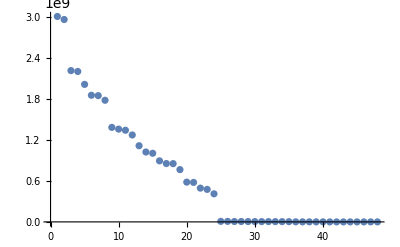

```mathematica
ListPlot[λ]
```

#### 1.2.2 Verify that the computed first eigenvector-eigenvalue pair satisfy the appropriate equation.

```mathematica
eigenval1 = Eigenvalues[A,1];
eigenvec1 = Eigenvectors[A,1];
```

#### 1.2.3 Verify that the eigenvectors are real and orthogonal.

```mathematica
OrthogonalMatrixQ[v]
```

True

```mathematica
Im[Norm[v]]
```

0

```mathematica
(* Zero indicates that there are no imaginary parts and eigenvectors are real*)
```

### 1.3 Is the matrix symmetric? Explain the connections between the singular values and eigenvalues

```mathematica
SymmetricMatrixQ[A]
```

True

The eigenvalues of the matrix’s SVD are the squares of its singular values.

## 2. Build a Tall Skinny random complex matrix

```mathematica
m = 50;
n = 2;
A = RandomReal[{-1,1},{m,n}];
```

### 2.1 Compute and plot the eigenvalues of A.(A^*A)^-1.A^*. Briefly describe the eigenvalues.

```mathematica
{λ,v} = Eigensystem[A.Inverse[Transpose[A].A].Transpose[A]];
```

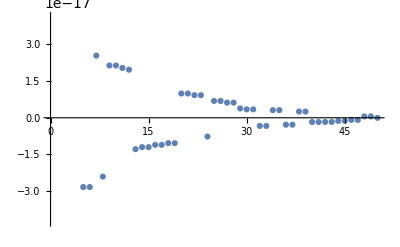

```mathematica
ListPlot[λ]
```

Eigenvalues are zero for tall skinny matrix and are nearly symmetric as it appears from the plot.

### 2.2 Construct H=I-2A.(A^*A)^-1.A^*.

```mathematica
H = IdentityMatrix[50]-2.A.Inverse[Transpose[A].A].Transpose[A];
```

#### 2.2.1 Compute H^*.H and describe it briefly.

```mathematica
Norm[Transpose[H].H]
```

1.

H^*H  gives identity matrix which means H is orthogonal matrix.

#### 2.2.2 Compute and plot the eigenvalues of H in the complex plane. Describe the eigenvalues briefly.

```mathematica
{λ,v} = Eigensystem[H];
```

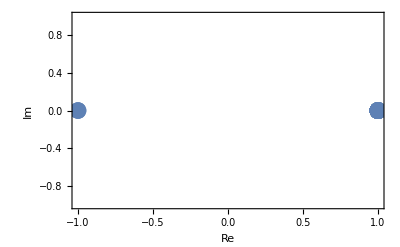

```mathematica
ListPlot[ReIm[λ],PlotStyle->PointSize[0.03],Frame->True,FrameLabel->{Re,Im}]
```

Eigenvalues are symmetric about real axis and the magnitude is equal to 1.